# Assignment 3

Karim Sobh
201700836

## Problem 1:

```mathematica
factorial[n_]:=(ClearAll[na,a,i];
na={1};a={1};
For[i=1,i≤n,i++,AppendTo[na,N[(N[na[[i]]]+1)]];AppendTo[a,N[a[[i]] na[[i+1]]]]];Print[a[[n]]])

factorial[5]
```

120.

```mathematica
ffactorial[n_]:=(m=2n-1;factorial[m])
ffactorial[3]
```

120.

```mathematica
ffactorial[n_]:=(m=2n-1;ClearAll[nna,aa,i];
nna={1};aa={1};
For[i=1,i≤m,i++,AppendTo[nna,N[(N[nna[[i]]]+2)]];AppendTo[aa,N[aa[[i]] nna[[i+1]]]]];Print[aa[[i+1]]]; factorial[m])
aa
nna
ffactorial[3]
Factorial[5]
Factorial[7]
Factorial[(2*3)-1]
```

{1,3.,15.,105.,945.,10395.}

{1,3.,5.,7.,9.,11.}

Part::partw: Part 7 of {1,3.,15.,105.,945.,10395.} does not exist.

{1,3.,15.,105.,945.,10395.}⟦7⟧

120.

120

5040

120

## Problem 2:

```mathematica
a1=NIntegrate[Cos[z Sin[θ]] Exp[y Cos[θ]]/Pi,{θ,0,Pi}]-> {y = 0.15, z =0.5}
a2=BesselJ[0,Sqrt[z^{2}-y^{2}]][[1]] -> {y = 0.15, z =0.5}
a1==a2
```

0.943929→{0.15,0.5}

0.943929→{0.15,0.5}

True

```mathematica
n1=NIntegrate[1/Sqrt[6-u^{2}],{u,2,Sqrt[6]}][[1]]
n2= N[ArcCot[Sqrt[2]]]
N[n1]==N[n2]
```

0.61548

0.61548

False

## Problem 3:

```mathematica
FindRoot[x == (1+1/x)^(x) ,{x,1}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of (1+1/x)^x.

Hold[{x→2.29317}]

## Problem 4:

```mathematica
(*This Program is to find the Maximum value of the flow represented by Q*)
ClearAll[θ,Q];
Q= (θ-Sin[θ])^(5/3)/θ^(2/3);
Simplify[Q]
theta=Range[0.1,2Pi,0.1];
QQ=0theta;Q1=0theta; Q2=0theta; 
Simplify[ D[Q,θ]]
Simplify[D[D[Q,θ],θ]]
Do[QQ[[i]]= ((theta[[i]]-Sin[theta[[i]]])^(5/3))/(theta[[i]]^(2/3)),{i,1,Length[theta]}]
l=Ordering[QQ,-1]
Angel=(theta[[l]]×180 Degree)/Pi
QQ;
Qm=FindMaxValue[{(θ-Sin[θ])^(5/3)/θ^(2/3),0≤θ≤2Pi},{θ,0.1}]
```

(θ-Sin[θ])^(5/3)/θ^(2/3)

((θ-Sin[θ])^(2/3) (3 θ-5 θ Cos[θ]+2 Sin[θ]))/(3 θ^(5/3))

(5 (2-θ^2+(-2+5 θ^2) Cos[2 θ]+6 θ^3 Sin[θ]-4 θ Sin[2 θ]))/(18 θ^(8/3) (θ-Sin[θ])^(1/3))

{53}

{5.3}

6.75886

## Problem 5:

```mathematica
fy=ArcTan[(a*Cot[x]*Sin[x]^(2)- b Cot[x])/(c+d Cos[2x])];
yl={0.0,0.09821,0.1843,0.2671,0.3384,0.426,0.5316,0.5845,0.6527,0.6865,0.8015,0.8265,0.7696,0.7057,0.4338,0.0};
xl={0.01,0.1141,0.2181,0.3222,0.4262,0.5303,0.6343,0.7384,0.8424,0.9465,1.051,1.155,1.259,1.363,1.467,1.571};

Data=Transpose@{xl,yl};
fit=FindFit[Data,fy,{a,b,c,d},x]
(*To Make sure our resukt fits, PS: Not exactly :'( *)
fy/.fit
yyy={0};
For[i=2,i<=Length[xl],i++,yyy=AppendTo[yyy,
ArcTan[(123.133*Cot[xl[[i]]]*Sin[xl[[i]]]^(2)-0.012102 Cot[xl[[i]]])/(85.8661+61.2723 Cos[2xl[[i]]])]]]
yyy
```

{a→123.133,b→0.012102,c→85.8661,d→61.2723}

ArcTan[(-0.012102 Cot[x]+123.133 Cos[x] Sin[x])/(85.8661+61.2723 Cos[2 x])]

{0,0.0946817,0.18155,0.267428,0.351817,0.434289,0.513869,0.589538,0.659403,0.720819,0.769165,0.795452,0.782929,0.694988,0.455377,-0.00101962}

## Problem 6:

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

InterpolatingFunction[…]

InterpolatingFunction[…]

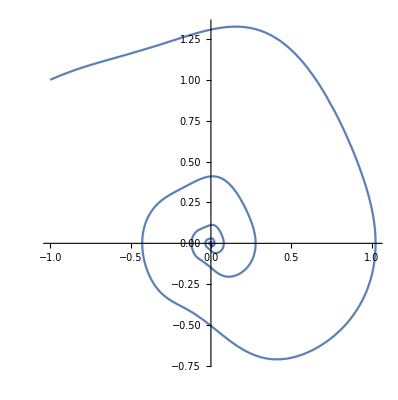

```mathematica
Clear[y1,y2];
ω=0.97;
ε=0.16;
γ=0.4;
(*x is y1,y is y2*)
L=Function[t,1+ε Sin[ω t+(9/8) Pi]^7];
sol=NDSolve[{y1'[t]==y2[t],y2'[t]==-(2 (L'[t]/L[t]) + γ  L[t])y2[t]-Sin[y1[t]]/L[t],y1[0]==-1,y2[0]==1},{y1,y2},{t,0,30}]
yy1=y1/. First@sol
yy2=y2/.First@sol
ParametricPlot[{yy1[t],yy2[t]},{t,0,30}, PlotRange->All]
```